```mathematica
(* This cell contains generic setup stuff to prepare for execution of the programs *)
ClearAll["Global`*"]; ParamsAreSet = False;
If[$VersionNumber < 6,(*then*) Print["These programs require Mathematica version 6 or greater."]; Abort[]];
(* If running from Notebook front end, set directory to Notebook's directory *)
If[Length[$FrontEnd] > 0, NBDir = SetDirectory[NotebookDirectory[]]];(* If running from the Notebook interface *)
If[Length[$FrontEnd] == 0,SetDirectory["/Volumes/Data/Work/BufferStock/BufferStockTheory/Latest/Code/Mathematica/Results/BufferStockTheory"]];
SaveFigs = False;
HomeDir = Directory[];
CodeDir = HomeDir<>"/../../CoreCode";
CDToHomeDir := SetDirectory[HomeDir];
CDToCodeDir := SetDirectory[HomeDir<>"/../../CoreCode"];

CDToCodeDir;
<< SetupModelSolutionRoutines.m;
<< SetParamsToBaselineVals.m;
CDToHomeDir;
aGridVecExcBotSmallLength = 10;
aGridVecExcBotLargeLength = 10;
ConstructLastPeriodAsSmoothedInfHorPFLiqConstrSolnJoinedAtPeriod[3];
SolveAnotherPeriod
```

```mathematica
VerboseOutput=True;Do[SolveAnotherPeriod,{10}]
```

Solved 10 periods.

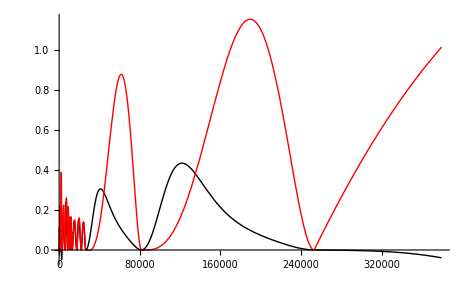

```mathematica
Plot[{nP[𝓋FromGapP[m]]-𝒸[m],nP[𝓋P[m]]-𝒸[m]},{m,mVecExcBot[[-1]]1.5,mVecExcBot[[1]]},PlotRange->All,PlotStyle->{Black,Red,Green,Blue}]
```

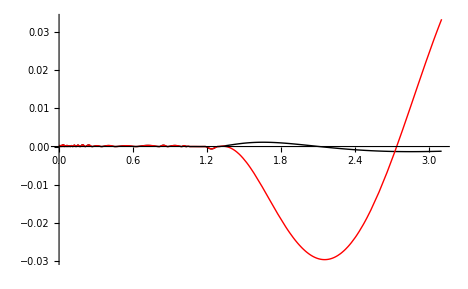

```mathematica
Plot[{nP[𝓋FromGapP[m]]-𝒸[m],nP[𝓋P[m]]-𝒸[m]},{m,mVecExcBot[[1]]0.1,2 mTarget},PlotRange->All,PlotStyle->{Black,Red,Green,Blue}]
```

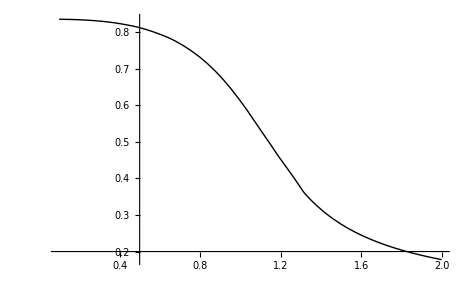

```mathematica
Plot[κ[m],{m,0.1,2}]
```

```mathematica
Animate[Plot[χFull[[n]][μ],{μ,μVecExcBot[[1]]-0.1,6(*μVecExcBot[[-1]]+0.1*)},PlotRange->{Automatic,{-0,-15}}],{n,2,Horizon,1},AnimationRunning->False]
```

```mathematica
Animate[Plot[𝒸[m,n],{m,0.01,5},PlotRange->{Automatic,{0,2}}],{n,0,Horizon,1},AnimationRunning->False]
```

```mathematica
Plot[{cLiqExact[m],𝒸Lim[m],𝒸LinearSplineFunc[[-1]][m],cLiqOrder1Func[m],𝒸[m]},{m,1,m♮},PlotStyle->{Black,Red,Green,Blue}]
```

-Graphics-

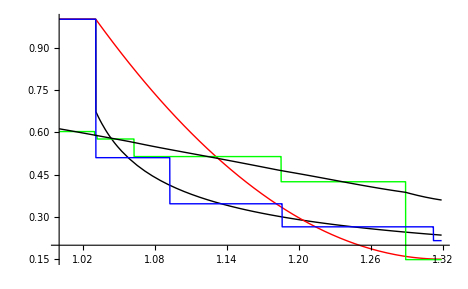

```mathematica
Plot[{κLiqExact[m],κLim[m],𝒸LinearSplineFunc[[-1]]'[m],cLiqOrder1Func'[m],κ[m]},{m,1.0,(*m♮*)mSplice},PlotStyle->{Black,Red,Green,Blue},PlotRange->All]
```

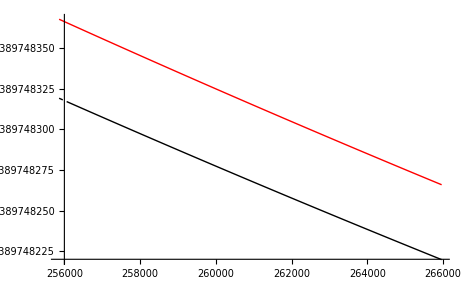

```mathematica
Plot[{κLim[m],κ[m]},{m,mLast-100,mLast+10000},PlotStyle->{Black,Red,Green},PlotRange->All]
```

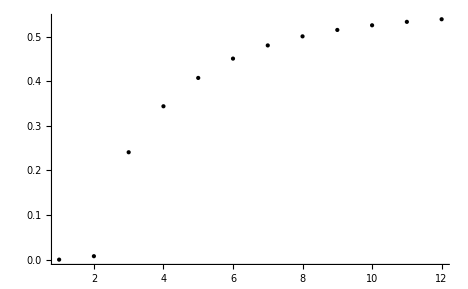

```mathematica
ListPlot[aTargetList,PlotRange->All]
```

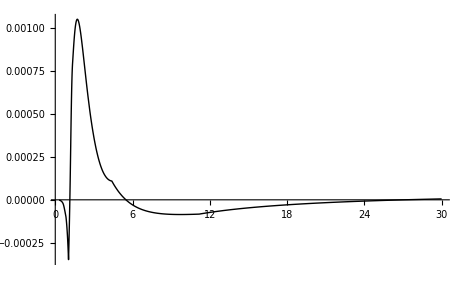

```mathematica
Plot[{κ[m,Horizon-1]-κ[m,Horizon-2]},{m,0.3,30},PlotRange->All]
```

```mathematica
Length[aGridVecIncBot]
```

20

```mathematica
VerboseOutput=True;SolveInfHorizToToleranceAtTarget[0.001]
```

With new shocks, adjusted Growth Patience Factor is 0.970097

-0.0560994 is latest tolerance for target change.

-0.0309194 is latest tolerance for target change.

-0.0185335 is latest tolerance for target change.

-0.0113035 is latest tolerance for target change.

-0.00690208 is latest tolerance for target change.

-0.00420222 is latest tolerance for target change.

-0.00255013 is latest tolerance for target change.

Solved 10 periods.

-0.00154336 is latest tolerance for target change.

-0.000932042 is latest tolerance for target change.

-0.000562091 is latest tolerance for target change.

-0.000338698 is latest tolerance for target change.

-0.000203987 is latest tolerance for target change.

-0.000122818 is latest tolerance for target change.

Converged.

With new shocks, adjusted Growth Patience Factor is 0.977819

-0.0163281 is latest tolerance for target change.

-0.0111081 is latest tolerance for target change.

-0.00765337 is latest tolerance for target change.

Solved 20 periods.

-0.0053117 is latest tolerance for target change.

-0.00370325 is latest tolerance for target change.

-0.0025896 is latest tolerance for target change.

-0.0018151 is latest tolerance for target change.

-0.00127453 is latest tolerance for target change.

-0.000896241 is latest tolerance for target change.

-0.000630986 is latest tolerance for target change.

-0.000444683 is latest tolerance for target change.

-0.00031365 is latest tolerance for target change.

-0.000221384 is latest tolerance for target change.

Converged.

With new shocks, adjusted Growth Patience Factor is 0.979199

Solved 30 periods.

-0.00413148 is latest tolerance for target change.

-0.00287473 is latest tolerance for target change.

-0.00201495 is latest tolerance for target change.

-0.00142231 is latest tolerance for target change.

-0.00101011 is latest tolerance for target change.

-0.000720954 is latest tolerance for target change.

-0.000516647 is latest tolerance for target change.

-0.00037144 is latest tolerance for target change.

Converged.

With new shocks, adjusted Growth Patience Factor is 0.979559

Solved 40 periods.

-0.001326 is latest tolerance for target change.

-0.000934322 is latest tolerance for target change.

Converged.

True